```mathematica
Exit[]
```

```mathematica
$Assumptions={_∈Reals, X0[x]∈Reals,Y0[x]∈Reals,aa>0,κ>0,β>0,Δ>0,lp>0,ϵ>0,λ[1]>0,λ[2]>0,λ[3]>0,Q1>0, μ>0,μ1>0,μ2>0,μ3>0,Δ>0,η>0,Px[x1]>0,Py[x1]>0,-3 K0[t]^2+Λ P0[t]<0,P0[t]>0,Sin[θ]>0};
```

## Kretschmann vs Δ

```mathematica
Get[NotebookDirectory[]<>"eoms.wl"];
Needs["DifferentialEquations`NDSolveProblems`"];
Needs["DifferentialEquations`NDSolveUtilities`"];
```

```mathematica
bdy0={Ex[x0]-> 3/2 (3/2)^(1/3) (√Rs (x0))^(4/3),Eϕ[x0]-> (3/2)^(1/3) √Rs (√Rs (x0))^(1/3),Kx[x0]-> Rs/(3 2^(2/3) 3^(1/3) (√Rs (x0))^(4/3)),Kϕ[x0]-> -((2/3)^(1/3) √Rs)/(√Rs (x0))^(1/3)};bdyKv0=Refine[{K1[z]-> (√Ex[z] Kx[z])/Eϕ[z],K2[z]-> Kϕ[z]/(√Ex[z]),v1[z]-> Log[Ex[z]],v2[z]-> Log[Eϕ[z]]}/.z-> x0/.bdy0,Assumptions->{x0>0,Δ>0,Rs>0}];
bdyKv={K1[z]==K1[x0],K2[z]==K2[x0],v1[z]==v1[x0],v2[z]==v2[x0]}/.bdyKv0/.z-> x0
```

{K1[x0]==1/(6 x0),K2[x0]==-2/(3 x0),v1[x0]==Log[3/2 (3/2)^(1/3) Rs^(2/3) x0^(4/3)],v2[x0]==Log[(3/2)^(1/3) Rs^(2/3) x0^(1/3)]}

```mathematica
bdyKv/.parameters//N
```

{K1[3.×10^8]==5.55556×10^-10,K2[3.×10^8]==-2.22222×10^-9,v1[3.×10^8]==40.3819,v2[3.×10^8]==20.4571}

```mathematica
xM=3*10^8;
parameters={a-> 1,β->1,Rs->10^9,Δ->0.15,t0->0,x0-> xM,μ0-> 0.1,λ0-> 0.1};
effeomODEKv={Table[eomKv[[i]]==0,{i,1,4}],bdyKv}/.parameters//Flatten;
nsolKv=NDSolve[effeomODEKv,{K1[z],K2[z],v1[z],v2[z]},{z,-1000,xM},Method->"ImplicitRungeKutta"]//Flatten
```

{K1[z]→InterpolatingFunction[…][z],K2[z]→InterpolatingFunction[…][z],v1[z]→InterpolatingFunction[…][z],v2[z]→InterpolatingFunction[…][z]}

General::munfl: Exp[-1208.96] is too small to represent as a normalized machine number; precision may be lost.

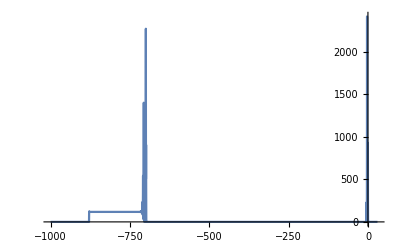

```mathematica
KretschmannN2=(Kretschmann/.{x-> t+z}/.chvarearly/.D[chvarearly, z]//Simplify)/.parameters/.nsolKv/.D[nsolKv, z]/.D[D[nsolKv, z], z];
Plot[KretschmannN2,{z,-1000,30},PlotRange->All]
```

```mathematica
Kre[15]={Max[ParallelTable[KretschmannN2,{z,-750,-660,gap}]],Max[ParallelTable[KretschmannN2,{z,-30,30,gap}]]}
```

{2379.13,2642.74}

```mathematica
Kre[14]={Max[ParallelTable[KretschmannN2,{z,-730,-650,gap}]],Max[ParallelTable[KretschmannN2,{z,-30,30,gap}]]}
```

{2735.59,3034.27}

```mathematica
Kre[13]={Max[ParallelTable[KretschmannN2,{z,-700,-630,gap}]],Max[ParallelTable[KretschmannN2/.y->z,{z,-30,30,gap}]]}
```

{3155.58,3482.13}

```mathematica
Kre[12]={Max[ParallelTable[KretschmannN2,{z,-700,-600,gap}]],Max[ParallelTable[KretschmannN2/.y->z,{z,-30,30,gap}]]}
```

{3735.3,4121.52}

```mathematica
Kre[11]={Max[ParallelTable[KretschmannN2,{z,-670,-600,gap}]],Max[ParallelTable[KretschmannN2/.y->z,{z,-30,30,gap}]]}
```

{4437.41,4916.42}

```mathematica
gap=0.001;
Kre[1]={Max[ParallelTable[KretschmannN2,{z,-300,-260,gap}]],Max[ParallelTable[KretschmannN2/.y->z,{z,-30,30,gap}]]}
```

{547900.,591165.}

```mathematica
gap=0.001;
Kre[2]={Max[ParallelTable[KretschmannN2,{z,-380,-320,gap}]],Max[ParallelTable[KretschmannN2/.y->z,{z,-30,30,gap}]]}
```

{135972.,148446.}

```mathematica
gap=0.001;
Kre[3]={Max[ParallelTable[KretschmannN2,{z,-450,-380,gap}]],Max[ParallelTable[KretschmannN2/.y->z,{z,-30,30,gap}]]}
```

{60290.7,65786.5}

```mathematica
gap=0.001;
Kre[4]={Max[ParallelTable[KretschmannN2,{z,-480,-420,gap}]],Max[ParallelTable[KretschmannN2/.y->z,{z,-30,30,gap}]]}
```

{33908.4,36985.6}

```mathematica
gap=0.001;
Kre[5]={Max[ParallelTable[KretschmannN2,{z,-500,-450,gap}]],Max[ParallelTable[KretschmannN2/.y->z,{z,-30,30,gap}]]}
```

{21625.,23583.8}

```mathematica
gap=0.001;
Kre[6]={Max[ParallelTable[KretschmannN2,{z,-550,-500,gap}]],Max[ParallelTable[KretschmannN2/.y->z,{z,-30,30,gap}]]}
```

{14986.7,16456.8}

```mathematica
gap=0.001;
Kre[7]={Max[ParallelTable[KretschmannN2,{z,-580,-500,gap}]],Max[ParallelTable[KretschmannN2/.y->z,{z,-30,30,gap}]]}
```

{11034.1,11997.4}

```mathematica
gap=0.001;
Kre[8]={Max[ParallelTable[KretschmannN2,{z,-600,-550,gap}]],Max[ParallelTable[KretschmannN2/.y->z,{z,-30,20,gap}]]}
```

{8373.91,9198.77}

```mathematica
gap=0.001;
Kre[9]={Max[ParallelTable[KretschmannN2,{z,-620,-550,gap}]],Max[ParallelTable[KretschmannN2/.y->z,{z,-30,20,gap}]]}
```

{6594.43,7273.28}

```mathematica
gap=0.001;
Kre[10]={Max[ParallelTable[KretschmannN2,{z,-650,-550,gap}]],Max[ParallelTable[KretschmannN2/.y->z,{z,-50,20,gap}]]}
```

{5370.29,5915.3}

```mathematica
KretschmannΔ=Table[Kre[i],{i,1,15}]
```

{{547900.,591165.},{135972.,148446.},{60290.7,65786.5},{33908.4,36985.6},{21625.,23583.8},{14986.7,16456.8},{11034.1,11997.4},{8373.91,9198.77},{6594.43,7273.28},{5370.29,5915.3},{4437.41,4916.42},{3735.3,4121.52},{3155.58,3482.13},{2735.59,3034.27},{2379.13,2642.74}}

```mathematica
Save[NotebookDirectory[]<>"KretschmannVsDelta(xM=3*10^8,Rs->10^9,Delta->0.01m,m=1--15,the second column is for the bounce at z=0).wl",KretschmannΔ]
```

```mathematica
KretschmannΔ2=Table[Kre[i][[2]],{i,1,15}]
```

{591165.,148446.,65786.5,36985.6,23583.8,16456.8,11997.4,9198.77,7273.28,5915.3,4916.42,4121.52,3482.13,3034.27,2642.74}

```mathematica
LinearModelFit[Transpose[{Log[Table[0.01m,{m,1,15}]],Log[KretschmannΔ2]}],x,x]
```

FittedModel[4.08145-1.99957 x]

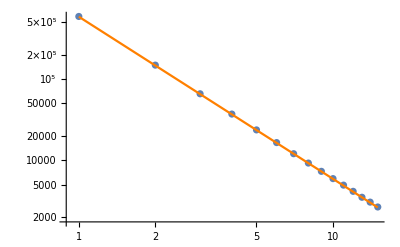

```mathematica
Show[ListLogLogPlot[KretschmannΔ2],LogLogPlot[ⅇ^4.072062792162703/(0.01x)^2,{x,1,15},PlotStyle->Orange]]
```

```mathematica
ⅇ^4.072062792162703//N
```

```mathematica
58.67787810430857/π^2
```

5.94531

```mathematica
KretschmannΔ1=Table[Kre[i][[1]],{i,1,15}]
```

{547900.,135972.,60290.7,33908.4,21625.,14986.7,11034.1,8373.91,6594.43,5370.29,4437.41,3735.3,3155.58,2735.59,2379.13}

```mathematica
LinearModelFit[Transpose[{Log[Table[0.01m,{m,1,15}]],Log[KretschmannΔ1]}],x,x]
```

FittedModel[3.96252-2.00893 x]

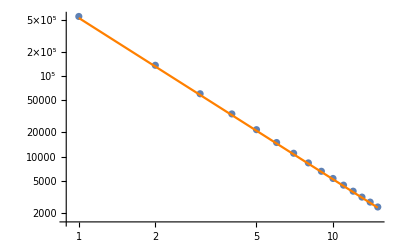

```mathematica
Show[ListLogLogPlot[KretschmannΔ1],LogLogPlot[ⅇ^3.9603419568011726/(0.01x)^2,{x,1,15},PlotStyle->Orange]]
```